```mathematica
A= 1;
sr=2;
```

```mathematica
ω=0.2;
```

```mathematica
L=5;
```

```mathematica
f[t_,r_]:=((r-t)^3 Exp[(-(r-t)^2)/(2 sr^2)])/r
(*f[t_,r_]:=Sin[(r-t)]^3/r*)
```

```mathematica
D[f[t,r],t]//Simplify
```

(ⅇ^(-(r-t)^2) (r-t)^2 (-3+2 r^2-4 r t+2 t^2))/r

```mathematica
Π[t_,r_]:=(ⅇ^(-(r-t)^2) (r-t)^2 (-3+2 r^2-4 r t+2 t^2))/r
```

```mathematica
D[f[t,r],r]
```

(ⅇ^(-(r-t)^2))/r-(ⅇ^(-(r-t)^2) (r-t))/r^2-(2 ⅇ^(-(r-t)^2) (r-t)^2)/r

```mathematica
Psi[t_,r_]:=(ⅇ^(-(r-t)^2))/r-(ⅇ^(-(r-t)^2) (r-t))/r^2-(2 ⅇ^(-(r-t)^2) (r-t)^2)/r
```

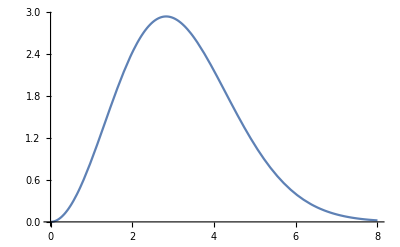

```mathematica
Plot[f[0,r],{r,0,8}]
```

```mathematica
g[t_,x_,y_,z_]:=f[t,r]/.{r->Sqrt[x^2+y^2+z^2]}
```

```mathematica
Π[t1_,x1_,y1_,z1_]:=D[g[t,x,y,z],t]/.{t->t1,x->x1,y->y1,z->z1}
Φx[t1_,x1_,y1_,z1_]:=D[g[t,x,y,z],x]/.{t->t1,x->x1,y->y1,z->z1}
Φy[t1_,x1_,y1_,z1_]:=D[g[t,x,y,z],y]/.{t->t1,x->x1,y->y1,z->z1}
Φz[t1_,x1_,y1_,z1_]:=D[g[t,x,y,z],z]/.{t->t1,x->x1,y->y1,z->z1}
```

```mathematica
Limit[Simplify[Φx[0,x,0,0]],{x->0}]
Limit[Simplify[Φy[0,x,0,0]],{x->0}]
Limit[Simplify[Φz[0,x,0,0]],{x->0}]
Limit[Simplify[Π[0,x,0,0]],x->0]
Limit[Simplify[g[0,x,0,0]],x->0]
```

Indeterminate

0

0

-2

0

```mathematica
D[g[t,x,y,z],{t,2}]-D[g[t,x,y,z],{x,2}]-D[g[t,x,y,z],{y,2}]-D[g[t,x,y,z],{z,2}]//FullSimplify
```

0

```mathematica
Plot3D[g[0,x,y,0],{x,-5,5},{y,-5,5},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[Π[7,k,n,L],{k,-5,5},{n,-5,5},PlotRange->All]
```

-Graphics3D-

```mathematica
Energy[t_]:=1/2 NIntegrate[Π[t,x,y,z]^2+Φx[t,x,y,z]^2+Φy[t,x,y,z]^2+Φz[t,x,y,z]^2,{x,-L,L},{y,-L,L},{z,-L,L},Method->"DoubleExponential"];
```

```mathematica
Energy[6]//Quiet
```

6.01289

```mathematica
e=Table[Energy[i],{i,0,14}]//Quiet//Chop
```

{5.92369,2.58582,12.861,12.3558,12.4664,10.4006,6.01289,2.33296,0.535528,0.0637049,0.00195265,1.71041×10^-6,0,0,0}

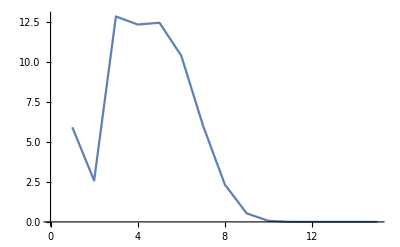

```mathematica
p1=ListLinePlot[e]
```

```mathematica
EnergyFlux[t_]:=
Quiet[NIntegrate[(Φx[t,L,y1,z1]+Φy[t,L,y1,z1]+Φz[t,L,y1,z1])Π[t,L,y1,z1] ,{y1,-L,L},{z1,-L,L},Method->"GlobalAdaptive"]]-Quiet[NIntegrate[(Φx[t,-L,y1,z1]+Φy[t,-L,y1,z1]+Φz[t,-L,y1,z1])Π[t,-L,y1,z1] ,{y1,-L,L},{z1,-L,L},Method->"GlobalAdaptive"]]+Quiet[NIntegrate[(
Φx[t,x1,L,z1]+Φy[t,x1,L,z1]+Φz[t,x1,L,z1])Π[t,x1,L,z1] ,{x1,-L,L},{z1,-L,L},Method->"GlobalAdaptive"]]-Quiet[NIntegrate[(
Φx[t,x1,-L,z1]+Φy[t,x1,-L,z1]+Φz[t,x1,-L,z1])Π[t,x1,-L,z1] ,{x1,-L,L},{z1,-L,L},Method->"GlobalAdaptive"]]+Quiet[NIntegrate[(
Φx[t,x1,y1,L]+Φy[t,x1,y1,L]+Φz[t,x1,y1,L])Π[t,x1,y1,L] ,{x1,-L,L},{y1,-L,L},Method->"GlobalAdaptive"]]-Quiet[NIntegrate[(
Φx[t,x1,y1,-L]+Φy[t,x1,y1,-L]+Φz[t,x1,y1,-L])Π[t,x1,y1,-L] ,{x1,-L,L},{y1,-L,L},Method->"GlobalAdaptive"]]
```

```mathematica
EnergyFluxS[t_,r_]:=NIntegrate[(Φx[t,r Cos[fi]Sin[th],r Sin[fi]Sin[th],r Cos[th]]Cos[fi]Sin[th]+Φy[t,r Cos[fi]Sin[th],r Sin[fi]Sin[th],r Cos[th]] Sin[fi]Sin[th]+Φz[t,r Cos[fi]Sin[th],r Sin[fi]Sin[th],r Cos[th]]Cos[th])Π[t,r Cos[fi]Sin[th],r Sin[fi]Sin[th],r Cos[th]] r^2 Sin[th] ,{fi,0,2π},{th,0,π},Method->"GlobalAdaptive"]
```

```mathematica
e2=Table[EnergyFlux[i],{i,0,14,0.1}]//Quiet//Chop
```

$Aborted

```mathematica
e22=Table[EnergyFluxS[i,5],{i,0,14,0.1}]//Quiet//Chop
```

{0,0,0,0,0,0,0,-4.42767×10^-10,-1.99215×10^-9,-8.56747×10^-9,-3.52079×10^-8,-1.38212×10^-7,-5.18105×10^-7,-1.8539×10^-6,-6.32949×10^-6,-0.0000206091,-0.0000639629,-0.000189114,-0.000532302,-0.00142531,-0.00362752,-0.00876676,-0.0200961,-0.0436378,-0.0896245,-0.173785,-0.317442,-0.544767,-0.87536,-1.31135,-1.82112,-2.32642,-2.70385,-2.81179,-2.54582,-1.90815,-1.05744,-0.297188,0.0210634,-0.3416,-1.36054,-2.70199,-3.83995,-4.30034,-3.90401,-2.85821,-1.62774,-0.661729,-0.156085,-0.0108651,0,-0.0110119,-0.160421,-0.6905,-1.7279,-3.09639,-4.33779,-4.94081,-4.62764,-3.51258,-2.04081,-0.759112,-0.0631903,-0.0557228,-0.563969,-1.2721,-1.87806,-2.19896,-2.19688,-1.94206,-1.55132,-1.13482,-0.767169,-0.482431,-0.283582,-0.156407,-0.0811816,-0.0397493,-0.0183961,-0.00806055,-0.00334848,-0.00132036,-0.0004947,-0.000176273,-0.0000597807,-0.0000193094,-5.94394×10^-6,-1.74468×10^-6,-4.88544×10^-7,-1.30567×10^-7,-3.33176×10^-8,-8.12057×10^-9,-1.8911×10^-9,-4.20908×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

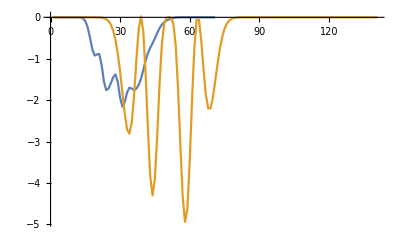

```mathematica
p2=ListLinePlot[{e2,e22}]
```

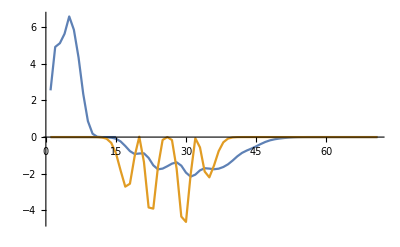

```mathematica
Show[p1,p2,PlotRange->All]
```

```mathematica
Sum[e2[[i]],{i,14}]
```

-0.0359353

```mathematica
Sum[e22[[i]],{i,14}]
```

-0.431393

```mathematica
Integrate[ ((x/r)*(x/r)+(y/r)(y/r)+(z/r)(z/r))r^2 Sin[th],{th,0,π},{phi, 0, 2π}]/.{(x^2+y^2+z^2)->r^2}//Simplify
```

4 π r^2

```mathematica
{x,y,z} = {r Cos[fi]Sin[th],r Sin[fi]Sin[th],r Cos[th]};
```

```mathematica
rvec = {x/r,y/r,z/r};
```

```mathematica
dSa = rvec r^2 Sin[th];
```

```mathematica
Integrate[rvec.dSa,{fi,0,2π},{th,0,π}]
```

4 π r^2